# Przeliczanie wyjść kontrolerów

```mathematica
sr[x_] = Piecewise[{{1, x≤ -1}, {1, x≤0}, {-x+1, x≤1},{0, x>1}}]
```

Piecewise[{{1, x≤-1||x≤0}, {1-x, x≤1}, {0, True}}]

```mathematica
sl[x_] = Piecewise[{{0, x≤ -1}, {x+1, x≤0}, {1, x≤1},{1, x>1}}]
```

Piecewise[{{0, x≤-1}, {1+x, x≤0}, {1, x≤1||x>1}, {0, True}}]

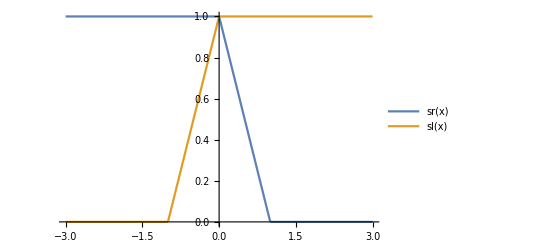

```mathematica
Plot[{sr[x],sl[x]}, {x,-3,3},PlotLegends->"Expressions"]
```